# Standardized ML approach

```mathematica
SeedRandom[2017]
```

```mathematica
unifyData[yes_List,no_List]:= Join[Thread[Table[yes[[x,All,All]],{x,Length[yes]}]-> "Yes"],Thread[Table[no[[x,All,All]],{x,Length[no]}]->"No"]]
```

```mathematica
partitionTrainTest[data_List,frac_Real]:={trainDataYesAndNo = RandomSample[data,Round@(Length[data]*frac)],
testDataYesAndNo = Complement[data,trainDataYesAndNo]}
```

```mathematica
rotateLabel[label_]:=Style[Rotate[label,Pi/4],30,Bold,Opacity[0.2],FontFamily->"Helvetica"];
showPerformance[dataTrain_List,dataTest_List]:=
BarChart[Query[All,ClassifierMeasurements[#,dataTest,"Accuracy"]&]@(Association@@(#->  Classify[dataTrain,Method->{#}]&/@{"LogisticRegression","Markov","NaiveBayes","NearestNeighbors","NeuralNetwork","RandomForest","SupportVectorMachine"})),ChartLabels->Placed[Automatic,Below,Rotate[#,Pi/2.4]&],ChartStyle->"DarkRainbow",LabelingFunction->(Placed[#,Above]&)]
```

```mathematica
reducedDataset = unifyData[reducedOxyNo80,reducedOxyYes80];
partitioned=partitionTrainTest[reducedDataset,0.8];
```

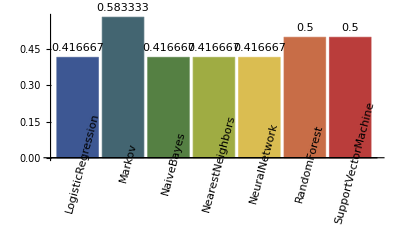

```mathematica
showPerformance[partitioned[[1]],partitioned[[2]] ]
```

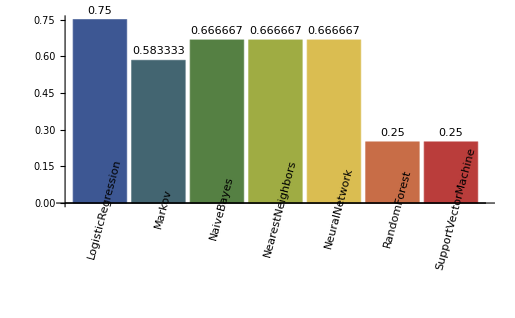

```mathematica
partitionFull = partitionTrainTest[fullDataYesAndNo,0.8];
showPerformance[partitionFull[[1]],partitionFull[[2]]]
```

```mathematica
unifyDataSARIMA[yes_List,no_List]:= Join[Thread[Table[yes[[x]],{x,Length[yes]}]-> "Yes"],Thread[Table[no[[x]],{x,Length[no]}]->"No"]]
reducedDatasetSARIMA = unifyDataSARIMA[coefYesSARIMA,coefNoSARIMA];
partitioned=partitionTrainTest[reducedDatasetSARIMA,0.7];
```

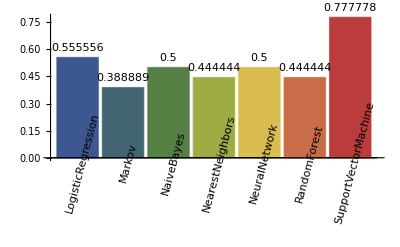

```mathematica
showPerformance[partitioned[[1]],partitioned[[2]] ]
```

```mathematica
wrpCustomArchYes[signal_List] :=Table[WarpingDistance[signal[[y]],archetypalMeanYes[[y]],DistanceFunction-> EuclideanDistance],{y,2}];
```

```mathematica
wrpCustomArchYes[signal_List] :=Table[WarpingDistance[signal[[y]],archetypalMeanYes[[y]]],{y,2}];
wrpCustomArchNo[signal_List] :=Table[WarpingDistance[signal[[y]],archetypalMeanNo[[y]]],{y,2}];
```

```mathematica
wrpFeat[signal_List]:= {wrpCustomArchYes[signal],wrpCustomArchNo[signal]}
```

```mathematica
wrpYes = Table[wrpFeat[reducedOxyYes80[[x]]],{x,30}];
```

```mathematica
wrpNo = Table[wrpFeat[reducedOxyNo80[[x]]],{x,30}];
```

```mathematica
unifyDataWrp[yes_List,no_List]:= Join[Thread[Table[yes[[x]],{x,Length[yes]}]-> "Yes"],Thread[Table[no[[x]],{x,Length[no]}]->"No"]]
```

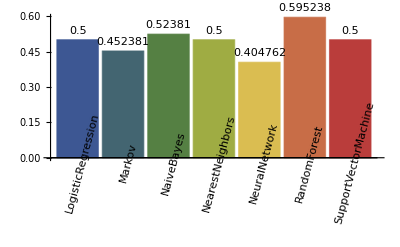

```mathematica
fullWrp = unifyDataWrp[wrpYes,wrpNo];
partWrp = partitionTrainTest[fullWrp,0.3];
showPerformance[partWrp[[1]],partWrp[[2]]]
```

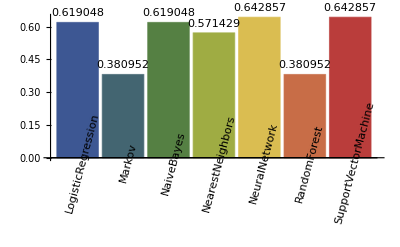

```mathematica
dataDistArchDrift;
partArch = partitionTrainTest[dataDistArchDrift,0.3];
showPerformance[partArch[[1]],partArch[[2]]]
```

```mathematica
leaveOneOutAccuracy[dataSet_] :=  Mean[
ClassifierMeasurements[Classify[Drop[dataSet,{#}]],Take[dataSet,{#}],"Accuracy"]&/@Range[Length[dataSet]]]
leaveOneOutAccuracy[dataSet_,str_] :=  Mean[
ClassifierMeasurements[Classify[Drop[dataSet,{#}],Method->str],Take[dataSet,{#}],"Accuracy"]&/@Range[Length[dataSet]]]
```

```mathematica
autoML[data_]:=  BarChart[leaveOneOutAccuracy[data,#]&/@ {"LogisticRegression","Markov","NaiveBayes","NearestNeighbors","NeuralNetwork","RandomForest","SupportVectorMachine"},
ChartLabels->Placed[{"LogisticRegression","Markov","NaiveBayes","NearestNeighbors","NeuralNetwork","RandomForest","SupportVectorMachine"},Below,Rotate[#,Pi/2.4]&],ChartStyle->"DarkRainbow",LabelingFunction->(Placed[#,Above]&)]
```

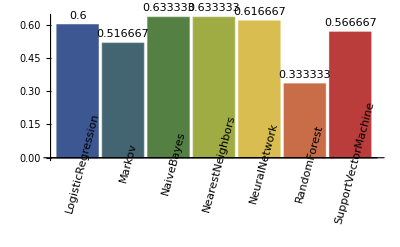

```mathematica
autoML[fullDataYesAndNo]
```